Solve for the EPs

```mathematica
S=Solve[-x^3+d x+c==0,x]//FullSimplify
```

{{x→-(2 3^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→((-1)^(1/3) (2 3^(1/3) d-(-2)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))}}

Plot the 3 branches to discover that it is the third (green) one we want

```mathematica
Plot3D[{x/.S[[1]],x/.S[[2]],x/.S[[3]]},{c,-4,4},{d,0,4}]
```

-Graphics3D-

Plot that branch with higher resolution

```mathematica
Plot3D[Evaluate[x/.S[[3]]],{c,-4,4},{d,0,4},MaxRecursion->7,WorkingPrecision->24]
```

-Graphics3D-

Plot slices for different d values to see the cross-sectional shape of this branch

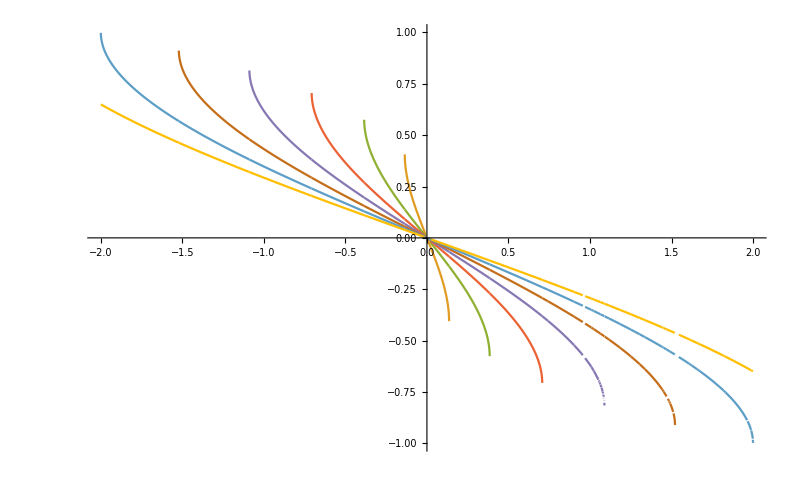

```mathematica
l1 = Plot[Evaluate[Table[Evaluate[x/.S[[3]]],{d,1/100000,4,1/2}]],{c,-2,2},PlotPoints->300]
```

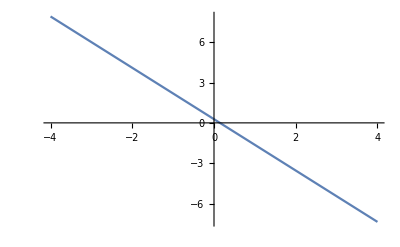

```mathematica
l2 =Plot[0.2745781780866053-1.9083893773871397 c,{c,-4,4},PlotPoints->300]
```

{d,1/100000,2,1/2}

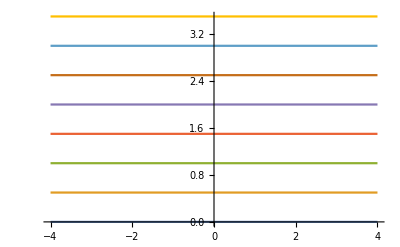

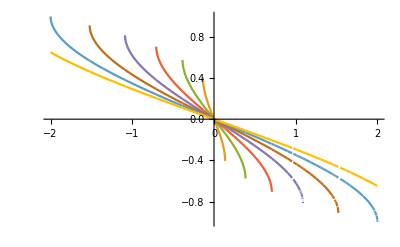

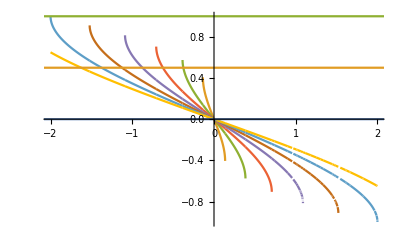

```mathematica
interval = {d, 1/100000,2,1/2}
l2=Plot[Evaluate[Table[Evaluate[d->0.2745781780866053-1.9083893773871397],{d, 1/100000,4,1/2}]],{c,-4,4},PlotPoints->300]
l1 = Plot[Evaluate[Table[Evaluate[x/.S[[3]]],{d, 1/100000,4,1/2}]],{c,-2,2},PlotPoints->300]
Show[l1,l2]
```

Let’s compute the central slope of this curve as a function of d

```mathematica
D[(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3)),c]//FullSimplify//ToRadicals
```

-((-3)^(1/3) (-3 √3 c+√(27 c^2-4 d^3)) (2 (-3)^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(2^(2/3) √(27 c^2-4 d^3) (-9 c+√(81 c^2-12 d^3))^(4/3))

```mathematica
-((-3)^(1/3) (-3 √3 c+√(27 c^2-4 d^3)) (2 (-3)^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(2^(2/3) √(27 c^2-4 d^3) (-9 c+√(81 c^2-12 d^3))^(4/3))/.c->0//FullSimplify
```

-((-1)^(1/3) ((-1)^(1/3) d+(-d^3)^(1/3)))/(2 (-d^3)^(2/3))

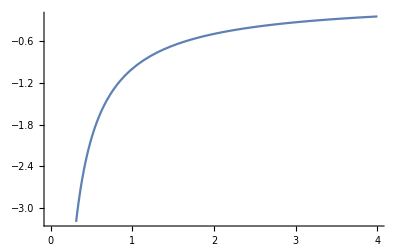

{1/100000→-1.63381,25001/100000→-1.63381,50001/100000→-1.63381,75001/100000→-1.63381,100001/100000→-1.63381,125001/100000→-1.63381,150001/100000→-1.63381,175001/100000→-1.63381,200001/100000→-1.63381,225001/100000→-1.63381,250001/100000→-1.63381,275001/100000→-1.63381,300001/100000→-1.63381,325001/100000→-1.63381,350001/100000→-1.63381,375001/100000→-1.63381}

```mathematica
Plot[-((-1)^(1/3) ((-1)^(1/3) d+(-d^3)^(1/3)))/(2 (-d^3)^(2/3)) ,{d,0,4}]
```

```mathematica
l2 =Plot[0.2745781780866053-1.9083893773871397 c,{c,-4,4},PlotPoints->300]
```

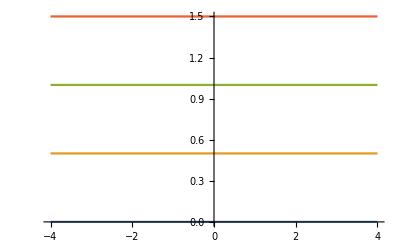

```mathematica
]
```